#### Utils

```mathematica
sampleDetRoot[det_,initList_]:=
First@MaximalBy[Quiet@Check[σ/.FindRoot[det,{σ,#}],-100-I]&/@initList,Re]
```

```mathematica
findDispRel[M_,params_,eq_,qRange_:{_,_,_}]:=With[{
MParams=M/.eq/.params
},
Table[
{qIter,sampleDetRoot[Det[MParams/.q->qIter],{0.1,0.1+0.1I,0.5,0.5+I,1.,1.+I,5.,5.+I,10.,10.+I,20.}]},
{qIter,Range@@qRange}
]
]
```

```mathematica
findDispRel[M_,params_,eq_,qRange_:{_,_,_},
"ApproxJacobian"->(approxJ_?MatrixQ)
]:=With[{
MParams=M/.eq/.params,
JApproxParams=approxJ/.eq/.params
},
Table[{
qIter,
σ/.FindRoot[
Det[MParams/.q->qIter],
{σ,First@MaximalBy[Eigenvalues[JApproxParams/.q->qIter],Re]},
Evaluated->False
]
},
{qIter,Range@@qRange}
]]
```

```mathematica
findLineDispRel[J_,params_,eq_,qRange_:{_,_,_}]:=With[{
JParams=J/.eq/.params
},
Table[
{qIter,First@MaximalBy[Eigenvalues[JParams/.q->qIter],Re]},
{qIter,Range@@qRange}
]
]
```

```mathematica
plotDispRel[dispRel_]:=ListPlot[Transpose[Thread[{#[[1]],ReIm@#[[2]]}]&/@dispRel],
Joined->True,
AxesLabel->{q,σ},
PlotLegends->{"Re(σ)","Im(σ)"}
]
```

#### Model setup

```mathematica
memVars={md,mde};
cytVars={cD,cDD,cE};
```

```mathematica
memReact={
(kD+kdD md)(cD-cDD)-kdE md cE,
kdE md cE-kde mde
};
cytCouple={
-(kD+kdD md)(cD-cDD)+kde mde,
kde mde,
kde mde-kdE md cE
};
```

```mathematica
params={
nD->400,nE->280,
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->10
};
```

#### Laterally homogeneous steady state

```mathematica
Γ[α_,q_]:=Sqrt[α+q^2]Tanh[Sqrt[α+q^2]h]
```

```mathematica
nSolveHSSEqns[params_]:=SortBy[Cases[
Chop@NSolve[
Join[memReact,
{
cytCouple[[1]],cytCouple[[3]],
DD Γ[λ/DD,0] cDD-cytCouple[[2]],
h cD+(md+mde)-h nD,
h cE+mde-h nE
}
]/.params,
Join[memVars,cytVars]
],
{HoldPattern[_->(_?(Im@#==0&&#≥0&))]..}
],
First
]
```

```mathematica
hssList=nSolveHSSEqns[params]
```

{{md→410.75,mde→2589.83,cD→99.942,cDD→68.493,cE→21.0171}}

#### Linear stability analysis

```mathematica
Jreact=D[Join[memReact,cytCouple],{Join[memVars,cytVars]}];
```

```mathematica
M=Jreact+DiagonalMatrix[{
-Dd q^2-σ,
-Dde q^2-σ,
-DD Γ[σ/DD,q],
-DD Γ[(σ+λ)/DD,q],
-DE Γ[σ/DE,q]
}];
```

```mathematica
dispRel=findDispRel[M,params,Last@hssList,{0,1.5,0.025}];
```

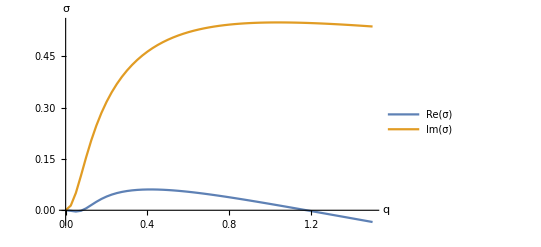

```mathematica
plotDispRel@dispRel
```

### Slow growth rate approximation

Develop the matrix M(σ) to first order in σ

```mathematica
M0=M/.σ->0;
```

```mathematica
M1=D[M,σ]/.σ->0;
```

We can then construct an eigenvalue problem for σ that yields the approximate solutions of M(σ)e=0:
Expand M

	0=M(σ)e≈(M_0+M_1 σ)e

Now multiply with M_1^-1 from the left

	(M_1^-1 M_0+σ)e≈0

Thus, the eigenvalues and eigenvectors of -M_1^-1 M_0 approximate the solution pairs (σ,e) of M(σ)e=0.

Note that M_1 becomes singular for q→0. Thus, the approximation only works for q≠0.

```mathematica
approxJacobian=-Inverse[M1].M0//Simplify;
```

```mathematica
dispRelApprox=findLineDispRel[approxJacobian,params,Last@hssList,{0.025,1.5,0.025}];
```

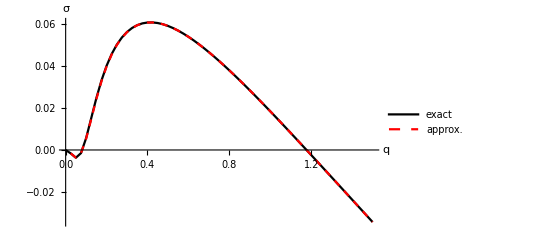

```mathematica
ListLinePlot[{
Re@dispRel,
Re@dispRelApprox
},
PlotStyle->{Black,Directive[Dashed,Red]},
AxesLabel->{q,σ},
PlotLegends->{"exact","approx."}
]
```

The slow growth rate approximation can be used to provide initial guesses for solving the full problem M(σ)e=0, for instance using an iterative method on the characteristic equation det M(σ)=0. This is implemented in the function findDispRel[] to which an approximate Jacobian can be supplied via the option “ApproxJacobian”.

Timing comparison:

```mathematica
findDispRel[M,params,Last@hssList,{0.025,1.5,0.025}];//AbsoluteTiming
```

{1.04784,Null}

```mathematica
findDispRel[M,params,Last@hssList,{0.025,1.5,0.025},"ApproxJacobian"->approxJacobian];//AbsoluteTiming
```

{0.054278,Null}